```mathematica
(*ISOTERMAL*)
time = 8000;
T =700;
R = 0.00008314;
k = 0.1;
Ureac = 0.41600;
order = 2;
PGas = 5;
Ao =1;
Vo = Ao*R*T/PGas;
VelO = 1;
VolInitial = 3000;
```

```mathematica
Rate = k*Exp[-Ureac/(R*T)]
s=NDSolve[{
A'[t] == -Rate*A[t]/V[t],
B'[t] == order*Rate*A[t]/V[t],
V'[t] == ( (-Rate*A[t]/V[t])+(order*Rate*A[t]/V[t]))*R*T/PGas,A[0]==Ao, B[0]==0,V[0]==Vo},{A,B,V},{t,0,time}]
```

0.0000786426

{{A→InterpolatingFunction[{{0., 8000.}}, <>],B→InterpolatingFunction[{{0., 8000.}}, <>],V→InterpolatingFunction[{{0., 8000.}}, <>]}}

```mathematica
Acceleration= Table[({V[t]/.s}-{V[t-1]/.s})/0.001,{t,1,time}];
```

```mathematica
Velocity = Table[Sum[Acceleration[[i]],{i,1,t}],{t,1,time}];
```

```mathematica
Distance1= Table[Sum[Velocity[[i]]+VelO,{i,1,t}],{t,1,time}];
```

```mathematica
Distance2 = Table[Distance1[[i]]+(VolInitial*({V[i-1]/.s}-{V[0]/.s})/({V[0]/.s})),{i,1,Length[Distance1]}];
```

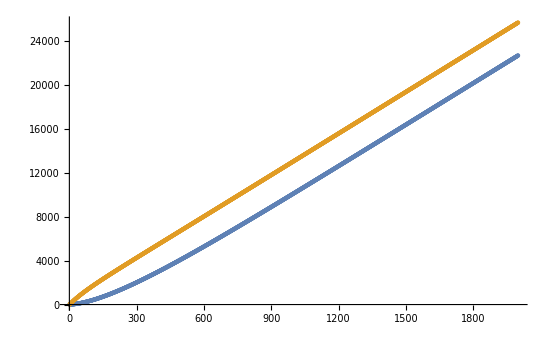

```mathematica
ListPlot[{Flatten[Distance1],Flatten[Distance2]}]
```